```mathematica
Tutorial of Lecture 1:Conceptual Introductions
```

## Exercise 1 Try it Yourself 1.2 [TB, by Shah Chapter 1]

Use a dataset that describes list price (X) and best price (i.e., cheapest) (Y) in $1000 for a new pick up truck. The dataset is available from  OA1 .2. Use this dataset to predict the best price of a pickup tuck that has been listed at $24, 000 by a dealer.

```mathematica
Obtaining the data :
```

If you downloaded data from Myaberdeen, and have place it in your computer, then set the directory to read the data such as bellow (but adapt for your own directory tree) :

```mathematica
Directory[]
```

/Users/murilo

```mathematica
SetDirectory["/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025-2026/DataDir/Lec1"]
```

/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025-2026/DataDir/Lec1

bellow extracts the sheet 1 in the excel file (or dimension 1 of the dataset)

```mathematica
dataset1=Import["OA1.2.xlsx",{"Data",1}]
```

{{X,Y},{12.4,11.2},{14.3,12.5},{14.5,12.7},{14.9,13.1},{16.1,14.1},{16.9,14.8},{16.5,14.4},{15.4,13.4},{17.,14.9},{17.9,15.6},{18.8,16.4},{20.3,17.7},{22.4,19.6},{19.4,16.9},{15.5,14.},{16.7,14.6},{17.3,15.1},{18.4,16.1},{19.2,16.8},{17.4,15.2},{19.5,17.},{19.7,17.2},{21.2,18.6}}

```mathematica
Dimensions[dataset1]
```

{24,2}

## Let us clean the data and eliminate the first row with the attributes of our data

```mathematica
dataset1=dataset1[[2;;,1;;2]]
```

{{12.4,11.2},{14.3,12.5},{14.5,12.7},{14.9,13.1},{16.1,14.1},{16.9,14.8},{16.5,14.4},{15.4,13.4},{17.,14.9},{17.9,15.6},{18.8,16.4},{20.3,17.7},{22.4,19.6},{19.4,16.9},{15.5,14.},{16.7,14.6},{17.3,15.1},{18.4,16.1},{19.2,16.8},{17.4,15.2},{19.5,17.},{19.7,17.2},{21.2,18.6}}

or use

```mathematica
Rest[dataset1]
```

{{14.3,12.5},{14.5,12.7},{14.9,13.1},{16.1,14.1},{16.9,14.8},{16.5,14.4},{15.4,13.4},{17.,14.9},{17.9,15.6},{18.8,16.4},{20.3,17.7},{22.4,19.6},{19.4,16.9},{15.5,14.},{16.7,14.6},{17.3,15.1},{18.4,16.1},{19.2,16.8},{17.4,15.2},{19.5,17.},{19.7,17.2},{21.2,18.6}}

## Let us explore the data

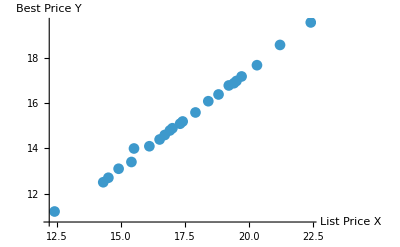

```mathematica
ListPlot[dataset1,AxesLabel->{"List Price X","Best Price Y"},PlotMarkers->Automatic]
```

The Plot shows a linear relationship, thus a linear regression will express well the relationship between the 2 datasets

## Let us model the data and estimate the linear relationship :

It should be of the form :

Y=aX+b

where a is the linear coefficient (the slope of the line) and b the constant term (intercept)

```mathematica
a=(Max[dataset1[[;;,2]]-Min[dataset1[[;;,2]]]])/(Max[dataset1[[;;,1]]-Min[dataset1[[;;,1]]]])
```

0.84

## Firstly, we estimate b we need to see where the line crosses the axis Y at X = 0

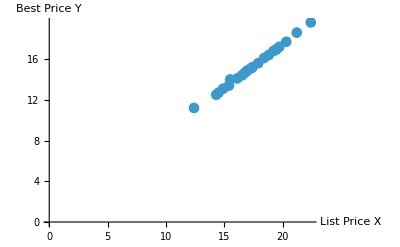

```mathematica
ListPlot[dataset1,AxesLabel->{"List Price X","Best Price Y"},PlotMarkers->Automatic, AxesOrigin->{0,0}]
```

Since  Mathematica  14.0, any  plot  now  by  default  has  a  "coordinate  mouseover"

Labels can be added to Frame, which is more standard in scientific presentations .

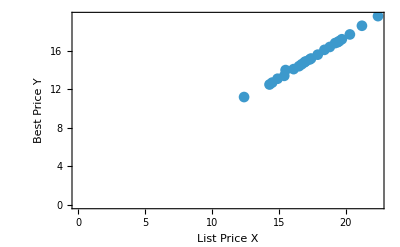

```mathematica
ListPlot[dataset1,Frame-> True, FrameLabel->{"List Price X","Best Price Y"},PlotMarkers->Automatic, AxesOrigin->{0,0}]
```

I estimate to be close to b=0.5

So, our model is

Y=0.84X+0.5

For a list price X = $24, 000, our predicted best price would be :

```mathematica
Y[X_]:=0.84X+0.5
```

```mathematica
Y[24]
```

20.66

Question: What needs to change to enter 24,000 instead of 24 as the argument of the function?

## Then, we improve on this prediction, by making a linear fit to the data by a linear regression.

```mathematica
LinearModelFit[dataset1,x,x]
```

FittedModel[…]

```mathematica
%36["ParameterTable"]
```

%36[ParameterTable]

The first "x" denotes the terms of a polynomial . For multilinear regression one could do {sin[x], cos[y]} . The second "x"  represents the argument of the function, which could be {x, y} for a multilinear regression .

So, input these fitted values into a Mathematica function :

```mathematica
Yexact[X_]:=0.85114X+0.4345
```

```mathematica
Yexact[24]
```

20.8619

## Exercise 2

## Hands-on Problem 1.1 [TB, by Shah Chapter 1]

Imagine you see yourself as the next Harland Sanders (founder of KFC) and want to learn about the poultry business at a much earlier age than Mr. Sanders did. You want to figure out what kind of feed can help grow healthier chickens. Use the dataset from OA 1.3.

## Obtaining the data :

```mathematica
dataset2=Import["https://raw.githubusercontent.com/vincentarelbundock/Rdatasets/master/csv/datasets/chickwts.csv"]//Dataset
```

## Let us clean the data and eliminate the attribute names (Weight, Feed)

```mathematica
dataset2=dataset2[[2;;,1;;]]
```

We could have eliminated the Header automatically:

```mathematica
dataset2=Rest[Import["https://raw.githubusercontent.com/vincentarelbundock/Rdatasets/master/csv/datasets/chickwts.csv"]]
```

{{1,179,horsebean},{2,160,horsebean},{3,136,horsebean},{4,227,horsebean},{5,217,horsebean},{6,168,horsebean},{7,108,horsebean},{8,124,horsebean},{9,143,horsebean},{10,140,horsebean},{11,309,linseed},{12,229,linseed},{13,181,linseed},{14,141,linseed},{15,260,linseed},{16,203,linseed},{17,148,linseed},{18,169,linseed},{19,213,linseed},{20,257,linseed},{21,244,linseed},{22,271,linseed},{23,243,soybean},{24,230,soybean},{25,248,soybean},{26,327,soybean},{27,329,soybean},{28,250,soybean},{29,193,soybean},{30,271,soybean},{31,316,soybean},{32,267,soybean},{33,199,soybean},{34,171,soybean},{35,158,soybean},{36,248,soybean},{37,423,sunflower},{38,340,sunflower},{39,392,sunflower},{40,339,sunflower},{41,341,sunflower},{42,226,sunflower},{43,320,sunflower},{44,295,sunflower},{45,334,sunflower},{46,322,sunflower},{47,297,sunflower},{48,318,sunflower},{49,325,meatmeal},{50,257,meatmeal},{51,303,meatmeal},{52,315,meatmeal},{53,380,meatmeal},{54,153,meatmeal},{55,263,meatmeal},{56,242,meatmeal},{57,206,meatmeal},{58,344,meatmeal},{59,258,meatmeal},{60,368,casein},{61,390,casein},{62,379,casein},{63,260,casein},{64,404,casein},{65,318,casein},{66,352,casein},{67,359,casein},{68,216,casein},{69,222,casein},{70,283,casein},{71,332,casein}}

Comment on format not being able any longer to extract first row: Link

## Let us separate the data by feed and clean it only using the numerical values :

one difficulty here is that the data for different feed is all in 2 columns

```mathematica
dataset2Horsebean=dataset2[[1;;10,2;;3]]
```

{{179,horsebean},{160,horsebean},{136,horsebean},{227,horsebean},{217,horsebean},{168,horsebean},{108,horsebean},{124,horsebean},{143,horsebean},{140,horsebean}}

Let us clear the feed name:

```mathematica
dataset2Horsebean=dataset2Horsebean[[1;;,1]]
```

{179,160,136,227,217,168,108,124,143,140}

```mathematica
dataset2Linseed=dataset2[[11;;22,2;;]]
```

{{309,linseed},{229,linseed},{181,linseed},{141,linseed},{260,linseed},{203,linseed},{148,linseed},{169,linseed},{213,linseed},{257,linseed},{244,linseed},{271,linseed}}

```mathematica
dataset2Linseed//Dataset;
```

```mathematica
dataset2Linseed=dataset2Linseed[[;;,1]]
```

{309,229,181,141,260,203,148,169,213,257,244,271}

```mathematica
dataset2Soybean=dataset2[[23;;36,2;;]]
```

{{243,soybean},{230,soybean},{248,soybean},{327,soybean},{329,soybean},{250,soybean},{193,soybean},{271,soybean},{316,soybean},{267,soybean},{199,soybean},{171,soybean},{158,soybean},{248,soybean}}

```mathematica
dataset2Soybean=dataset2Soybean[[;;,1]]
```

{243,230,248,327,329,250,193,271,316,267,199,171,158,248}

```mathematica
dataset2Sunflower=dataset2[[37;;48,2;;]]
```

{{423,sunflower},{340,sunflower},{392,sunflower},{339,sunflower},{341,sunflower},{226,sunflower},{320,sunflower},{295,sunflower},{334,sunflower},{322,sunflower},{297,sunflower},{318,sunflower}}

```mathematica
dataset2Sunflower=dataset2Sunflower[[;;,1]]
```

{423,340,392,339,341,226,320,295,334,322,297,318}

```mathematica
dataset2Meatmeal=dataset2[[49;;59,2;;]]
```

{{325,meatmeal},{257,meatmeal},{303,meatmeal},{315,meatmeal},{380,meatmeal},{153,meatmeal},{263,meatmeal},{242,meatmeal},{206,meatmeal},{344,meatmeal},{258,meatmeal}}

```mathematica
dataset2Meatmeal=dataset2Meatmeal[[;;,1]]
```

{325,257,303,315,380,153,263,242,206,344,258}

```mathematica
dataset2Casein=dataset2[[60;;71,2;;]]
```

{{368,casein},{390,casein},{379,casein},{260,casein},{404,casein},{318,casein},{352,casein},{359,casein},{216,casein},{222,casein},{283,casein},{332,casein}}

```mathematica
dataset2Casein=dataset2Casein[[;;,1]]
```

{368,390,379,260,404,318,352,359,216,222,283,332}

Let us explore our data

```mathematica
Mean[dataset2Casein]//N
```

323.583

```mathematica
Mean[dataset2Horsebean]//N
```

160.2

```mathematica
Mean[dataset2Meatmeal]//N
```

276.909

```mathematica
Mean[dataset2Linseed]//N
```

218.75

```mathematica
Mean[dataset2Soybean]//N
```

246.429

```mathematica
Mean[dataset2Sunflower]//N
```

328.917

Assuming the Mean Weight to be an indication of a Healthy chicken, you would conclude that Sunflower is the best feed

Still data difficult to compare as calculations were done, and not automated.

## Now, let us make a Table for minimal, mean, and maximal values, but with a bit more automation

```mathematica
cc={ dataset2Casein,dataset2Horsebean, dataset2Meatmeal, dataset2Linseed,dataset2Sunflower,dataset2Soybean }
```

{{368,390,379,260,404,318,352,359,216,222,283,332},{179,160,136,227,217,168,108,124,143,140},{325,257,303,315,380,153,263,242,206,344,258},{309,229,181,141,260,203,148,169,213,257,244,271},{423,340,392,339,341,226,320,295,334,322,297,318},{243,230,248,327,329,250,193,271,316,267,199,171,158,248}}

```mathematica
Mean[cc[[1]]]//N
```

323.583

```mathematica
Table[{Min[cc[[i]]],Mean[cc[[i]]],Max[cc[[i]]]},{i,1,6}]//N
```

{{216.,323.583,404.},{108.,160.2,227.},{153.,276.909,380.},{141.,218.75,309.},{226.,328.917,423.},{158.,246.429,329.}}

```mathematica
tabela=%
```

{{216.,323.583,404.},{108.,160.2,227.},{153.,276.909,380.},{141.,218.75,309.},{226.,328.917,423.},{158.,246.429,329.}}

```mathematica
tabela=Prepend[tabela,{Min, Mean,Max}]
```

{{Min,Mean,Max},{216.,323.583,404.},{108.,160.2,227.},{153.,276.909,380.},{141.,218.75,309.},{226.,328.917,423.},{158.,246.429,329.}}

```mathematica
TableForm[tabela]
```

Min | Mean | Max
216. | 323.583 | 404.
108. | 160.2 | 227.
153. | 276.909 | 380.
141. | 218.75 | 309.
226. | 328.917 | 423.
158. | 246.429 | 329.

## Visualize these values

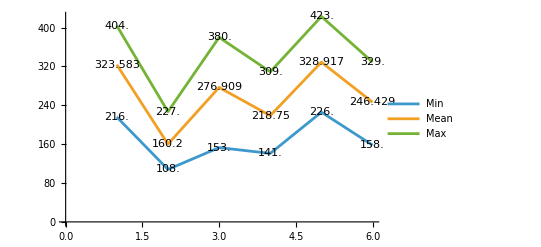

```mathematica
ListLinePlot[{tabela[[2;;,1]],tabela[[2;;,2]],tabela[[2;;,3]]},LabelingFunction->Center, PlotLegends->{Min,Mean,Max}]
```

Casein, Horsebean, Meatmeal, Linseed, Sunflower, Soybean

Let us now add FrameTicks to localize the feed:

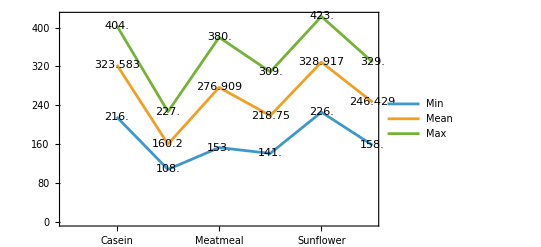

```mathematica
ListLinePlot[{tabela[[2;;,1]],tabela[[2;;,2]],tabela[[2;;,3]]},LabelingFunction->Center, PlotLegends->{Min,Mean,Max},Frame-> True,FrameTicks->{{Automatic,None},{{{1,"Casein"},{2,"Horsebean"},{3,"Meatmeal"},{4,"Linseed"},{5,"Sunflower"},{6,"Soybean"}},None}}]
```

Notice FrameTick -> {{Automatic, None}} {{Automatic, None}}, places Ticks on the usual {left, right} vertical and {bellow, above} horizontal axes .

## Make conclusions

Go to Sunflower: If goal is to maximize meat production, Sunflower produces chickens with large average and also largest Max weight, and assuming that mean weight is a good measure of healthy, Sunflower is the best feed.

Go to Casein: However, if you intend to sell your chicken for some markets, for example the EU, you have to abide by regulations such as a maximal variation of weights for the chickens. Casein has a slightly small mean as compared to Sunflower, but produces chickens with smallest variation in weight (404-216) as compared to the ones fed with Sunflower (423-226).

## We could have done this analysis quicker

```mathematica
dataset2=Import["https://raw.githubusercontent.com/vincentarelbundock/Rdatasets/master/csv/datasets/chickwts.csv",{"Dataset"},"HeaderLine"-> 1]
```

```mathematica
Dimensions[dataset2]
```

{71,3}

```mathematica
gathered=GatherBy[dataset2,#[[3]]&]
```

```mathematica
gathered[[3]][1,All];
```

```mathematica
gathered[[1]]
```

```mathematica
Dimensions[gathered]
```

{6}

To extract the weights from the horsebean :

```mathematica
Dimensions[gathered[[3]]]
```

{14,3}

```mathematica
gathered[[3]][[All,2]]
```

So, compute everything by :

```mathematica
Table[{gathered[[i]][[1,3]],Min[gathered[[i]][[All,2]]],Mean[gathered[[i]][[All,2]]],Max[gathered[[i]][[All,2]]]},{i,1,6}]//N//Dataset
```

## One could also select data for feeds using Select

```mathematica
dataset2=Import["https://raw.githubusercontent.com/vincentarelbundock/Rdatasets/master/csv/datasets/chickwts.csv"]
```

{{rownames,weight,feed},{1,179,horsebean},{2,160,horsebean},{3,136,horsebean},{4,227,horsebean},{5,217,horsebean},{6,168,horsebean},{7,108,horsebean},{8,124,horsebean},{9,143,horsebean},{10,140,horsebean},{11,309,linseed},{12,229,linseed},{13,181,linseed},{14,141,linseed},{15,260,linseed},{16,203,linseed},{17,148,linseed},{18,169,linseed},{19,213,linseed},{20,257,linseed},{21,244,linseed},{22,271,linseed},{23,243,soybean},{24,230,soybean},{25,248,soybean},{26,327,soybean},{27,329,soybean},{28,250,soybean},{29,193,soybean},{30,271,soybean},{31,316,soybean},{32,267,soybean},{33,199,soybean},{34,171,soybean},{35,158,soybean},{36,248,soybean},{37,423,sunflower},{38,340,sunflower},{39,392,sunflower},{40,339,sunflower},{41,341,sunflower},{42,226,sunflower},{43,320,sunflower},{44,295,sunflower},{45,334,sunflower},{46,322,sunflower},{47,297,sunflower},{48,318,sunflower},{49,325,meatmeal},{50,257,meatmeal},{51,303,meatmeal},{52,315,meatmeal},{53,380,meatmeal},{54,153,meatmeal},{55,263,meatmeal},{56,242,meatmeal},{57,206,meatmeal},{58,344,meatmeal},{59,258,meatmeal},{60,368,casein},{61,390,casein},{62,379,casein},{63,260,casein},{64,404,casein},{65,318,casein},{66,352,casein},{67,359,casein},{68,216,casein},{69,222,casein},{70,283,casein},{71,332,casein}}

```mathematica
Select[dataset2,#[[3]]=="horsebean"&]
```

{{1,179,horsebean},{2,160,horsebean},{3,136,horsebean},{4,227,horsebean},{5,217,horsebean},{6,168,horsebean},{7,108,horsebean},{8,124,horsebean},{9,143,horsebean},{10,140,horsebean}}